# CSci5105: Programming Assignment 3 (A Simple MapReduce-like Computation Framework)

## Kambala Balasubrahmanyam and Daniel DaCosta

## Introduction

This document describes the programming assignment three submission for the group composed of Kambala Balasubrahmanyam and Daniel DaCosta. This assignment required that a group implement a MapReduce framework that could be used to evaluate performance with respect to load balancing and fault tolerance. 

This implementation is expected to operate flawlessly and has been tested thoroughly. Please contact one of us if this is not the case.

## Assumptions, Caveats, and Terminology

• Job: A list of integers to be sorted.
• Task: A subset of a Job.
• Client: An interface to submit Jobs and receive Job responses.
• ComputeNode: Can sort and merge tasks, can accept/reject Tasks based on load, and can fail probabilistically.
• Server: An interface for submitting Jobs, marshalling Tasks between ComputeNodes and a Client.
• Data is read from a file by the Client.
• Data is passed between the Server and ComputeNodes as lists.
• The Server may only accept one Job at a time.
• ComputeNodes will fail only after a sorting Task has been assigned to it.
• When ComputeNodes fail they do not return.
• All ComputeNodes must register before submission of a Job by a Client.
• Tasks are only transfered due to load prior to Task execution. If load exceeds load threshhold during execution the Task will not be reassigned.
• If no other ComputeNodes will accept a Task reassignment, the over-loaded ComputeNode will execute the Task.
• Load is simulated via a Guassian or Constant (as explained by Dr. Chandra in class)

## Design

As discussed in the problem description there are three major types of components: Client, Server, and ComputeNodes.
All communication is done via RMI.
The basic control flow for Job completion is shown below.
-Graphics-

### Client

The Client has three modes of operation: Job submission, Server statistics querying, ComputeNode statistics querying.
Job submission reads a file of integers separated by newlines. This file is converted to a list and submited to the server.
Querying for Server or ComputeNode statistics is done via contacting either the Server and/or ComputeNode. In the case of ComputeNode statistics, the Client will lookup the ComputeNode address with a ComputeNode ID through an interface provided by the Server. Once the address has been found, it will contact the ComputeNode directly for statistics querying.

### Server

The Server organizes a Job into a set of sort Tasks and assigns them to ComputeNodes. When a Job is submitted by a Client, it is divided into equally sized sort Tasks according to how many ComputeNodes have registered prior to the Client submitting the Job. These sort Tasks are assigned to ComputeNodes.

ComputeNodes are expected to check-in (via a heartbeat) with the Server periodically. When a ComputeNode fails to check-in, it is considered dead. If a ComputeNode is dead, the Server will re-assign its sort Tasks to another ComputeNode. If no ComputeNodes remain, the Server will notify the Client that the Job failed to execute.

The Server waits for all outstanding sort Tasks to complete. When this occurs, the Server constructs a merge Task and assigns it to one ComputeNode. When the merge Task is complete, the Server will submit the result to the Client as a list.

The Server maintains statistics that can be queried by the Client.

### ComputeNode

ComputeNodes are the most complex components in this System. On startup, they register with the Server and are assigned a ID. From this point on they are expected to check-in with the Server periodically.

When assigned a sort Task, the ComputeNode checks whether its load is below some threshhold set either through a command-line argument or a configuration file. If it is below this threshhold, sorting begins. If not, the Client will search for a peer ComputeNode willing to accept the sort Task. If one is found, the sort Task is re-assigned. If none are found, the sort Task is executed. Processor load is simulated based on command-line arguments. The two simulation arguments correspond to a constant value or a randomly chosen value based on a Gaussian distribution. For the latter, a mean and variance must be provided.

A ComputeNode may fail if it is currently executing a sort Task. Failure is probabilistic and can be set via command-line arguments or through a configuration file. The sort Task is forced to take at least two seconds. The failure test executes every one second. Therefore each ComputeNode had at least two chances to fail during a sort Task. 

Completed sort Tasks are returned to the Server.

When assign a merge Task, the ComputeNode merges it and returns it to the Server.

Each sort and merge Task is allocated in its own thread.

## Testing

Testing was done almost exclusively in an automated fashion. Due to load simulation parameters, incorrect operation could be repeated with some accuracy.

Our testing regime involved two scripts. The RunTest.sh script would run a test with an arbitrary number of ComputeNodes with potentially different fail, load, and threshhold parameters. This script is employed by TestBattery.sh to systematically explore  the parameter space. Correct operation can generally be determined by Job completion or correct sort results. The latter is checked against the standard UNIX sort utility. Our submitted implementation has operated correctly under all tested scenarios. 

What follows are the parameters explored by TestBattery.sh(the current value sets are in brackets):
• Number of ComputeNodes [1,2,4,8]
• Fail Probabilities [0 2 4 8 16 32]
• Load Threshhold [100 80 60 50]
• Cardinality of Sort Set [500]
• Gaussian Load Simulator [(mean=50,variance=10)]
• Iterations per-parameter point [3]

For any given test, all ComputeNodes had the same parameters.
For each test, the output from all components were collect in the results directory.

## Performance Evaluation

In the Testing Section, an automated testing script was described. This script was also used to generate performance data.
In this section, a few interesting charts will be exposed.  All of the data that will be charted was retrieved from performance measurements where the Client, Server, and ComputeNode were on the same host.

The first results we will look at is strict sorting performance as a fucntion of the number of ComputeNodes. The results are predictably poor. Sorting is a relatively easy task at small input sizes, the overhead of marshalling the data to more ComputeNodes overcomes the benefit of concurrency. This marshalling penalty is most noticeable prior to the merge Task. The server needs to wait for eight different sort Tasks(in the worst case) to complete before being able to merge.

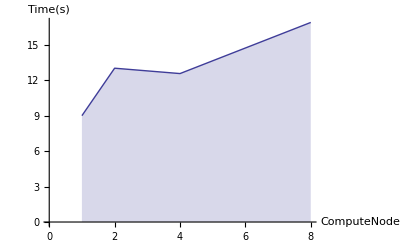

```mathematica
SetDirectory[ NotebookDirectory[] ];
data = Import ["results/results.csv"];
data = Map[Join[Take [#,{5,7}],Take[#,{9,10}]] &, data];
a = GatherBy[Sort[data],Last];
a = a[[1,All]];
b = Map[Join[Take[#,{3}],Take[#,{4}]] &,a];
c = GatherBy[b,First];
c=  Map [ {First[First[#]],Median[Last[#]]} &, c];
ListLinePlot[c,Filling -> Axis, AxesLabel -> {"ComputeNodes","Time(s)"}]
```

I assume a goal of this assignment was to impress upon us how failure recovery impacts performance. The next chart illustrates the intuitive notion that as ComputeNode failure probability increases, so will Job time. The Server must first notice that a ComputeNode has not checked in and then re-assign the failed ComputeNode’s Tasks. In otherwords, the cost of robustness is paid in performance efficiency.

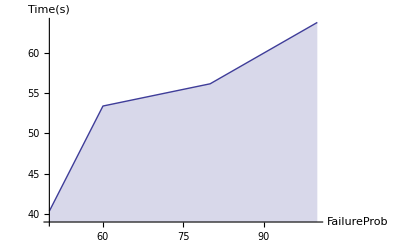

```mathematica
a = GatherBy[Sort[data],Last];
a = a[[1,All]];
b = Map[Join[Take[#,{2}],Take[#,{4}]] &,a];
c = GatherBy[Sort[b],First];
c=  Map [ {First[First[#]],Median[Last[#]]} &, c];
ListLinePlot[c,Filling -> Axis, AxesLabel -> {"FailureProb","Time(s)"}]
```

The benefits of multiple ComputeNodes can be seen in robustness to failure.  This final histogram shows how the number of successfully executed Jobs increased with the number of ComputeNodes.

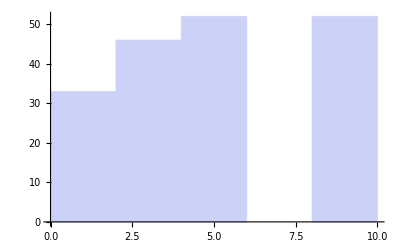

```mathematica
a = GatherBy[Sort[data],Last];
a = a[[1,All]];
b = Map[Join[{First[#]},Take[#,{4}]] &,a];
b = Sort[Map[First[Take[#,{3}]] &,a]];
Histogram[b,4]
```